#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-17);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v24/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v24/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

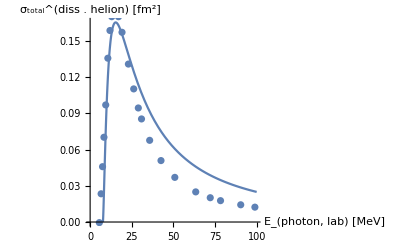

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);


evv=Eigenvalues[evm=(Transpose[invtrafma].norm).invtrafma];
Print["Min[Re] = ",Min[Re[evv]]];
Print["Max[Im] = ",Max[Im[evv]]];
evm=Chop[evm,10^(-6)];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}]

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3LSdims=Import["../basis_struct/LITbas_dims_J0.5_npp0.5^+.dat","Data"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

#### The initial state (helion ground state ^3 He ) -- in bare RGM Basis

B(^3He) = -5.64163

Dim_full^helion = 288

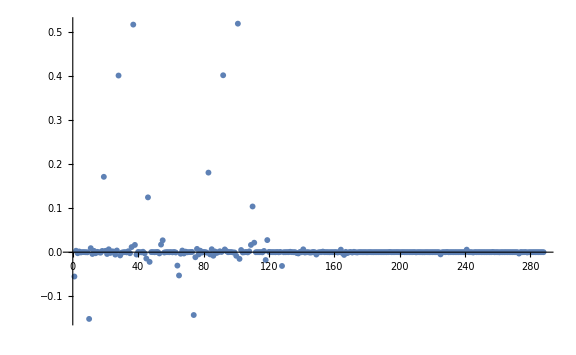
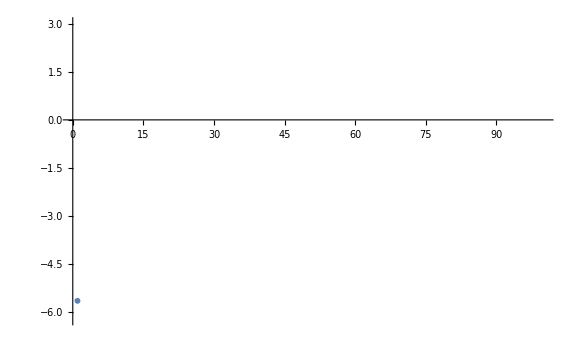
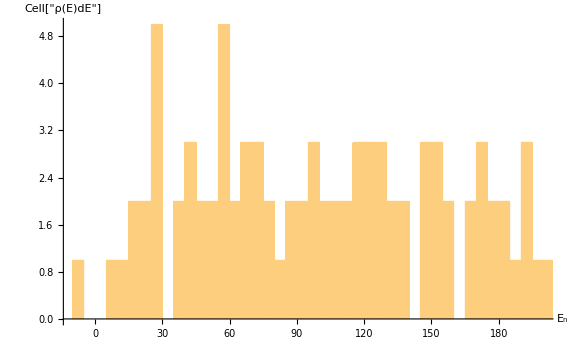
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVbare=Sort[Transpose[Eigensystem[{He3Ham,He3Norm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0bare=orderedEVbare[[1,1]];v0bare=orderedEVbare[[1,2]];

dE=5;
Print["B(^3He) = ",e0bare];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]]]

Grid[{{
ListPlot[Re[v0bare],PlotRange->Full,AxesLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVbare[[All,1]],PlotRange->{{0,100},{1.1 e0bare,3}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVbare[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"45d96bd0-ae25-4b28-924c-9abe19d2b34e"]"}]
}}]
```

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

min/max: {7.83599×10^-14,413463.}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

Min[Re] = 0.0427753

Max[Im] = 2.20851×10^-9

B(^3He) = -5.64163

Dim_full^helion = 288=^!288   ;     Dim_(non - singular)^helion = 288

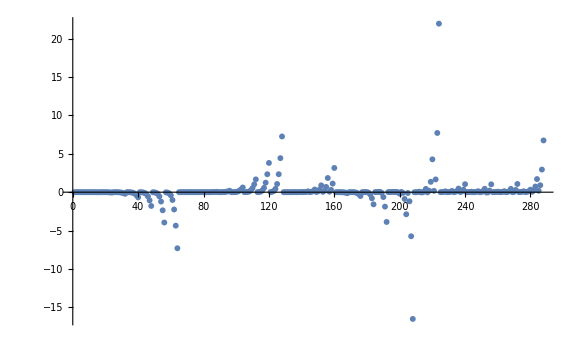
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
orderedEVSYHe3=Sort[Transpose[Eigensystem[{tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2,Transpose[He3Nmhi].He3Norm.He3Nmhi}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0=orderedEVSYHe3[[1,1]];v0=orderedEVSYHe3[[1,2]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]

fullv0=He3Nmh.v0;
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm-Eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{1.1 e0,3}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];

FinalStateLSdims=Flatten[Import["../basis_struct/LITbas_dims_J0.5_0.5^-.dat","Data"]];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

N_final = {503}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

J=0.5:  E_0=-0.976121

Final-state structure: {64,64,40,40,40,40,40,35,35,35,35,35}

{1.32976,1.33361,0.0000686211,0.000580758,0.00385121,1.42949×10^-6,0.000635318,0.000159435,1.42041×10^-6,0.0000171682,0.0000772437,0.0000228977}

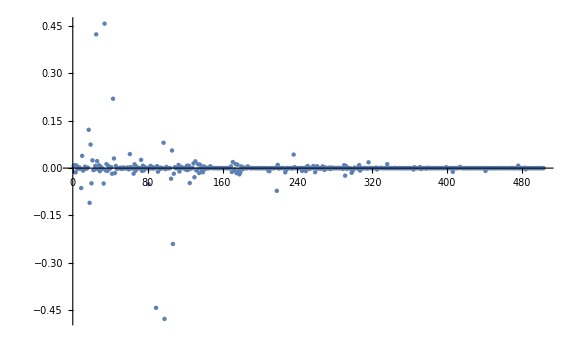
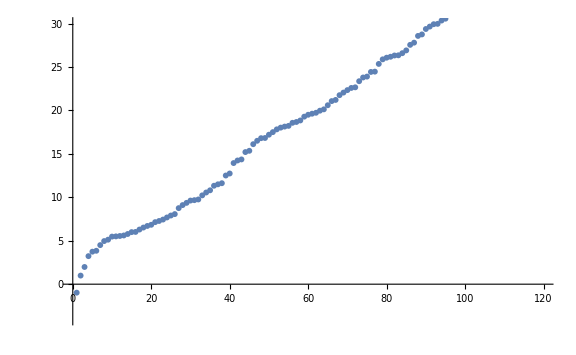
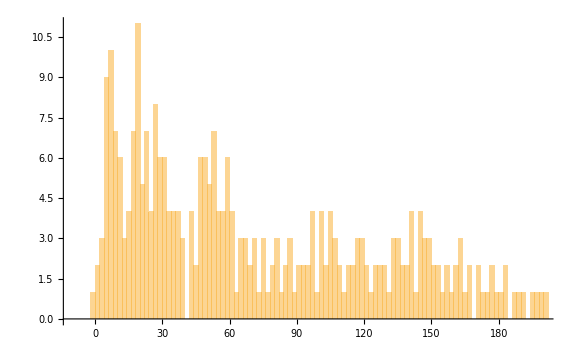
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
orderedEVbareOut=Sort[Transpose[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVbareOut[[1,1]];v0l=orderedEVbareOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];

Print["Final-state structure: ",FinalStateLSdims];
typ=Table[v0l[[If[n==0,0,Accumulate[FinalStateLSdims][[n]]]+1;;Accumulate[FinalStateLSdims][[n+1]]]],{n,0,Length[FinalStateLSdims]-1}];
Print[Total[#]&/@typ^2];

AppendTo[fullv0l,v0l];
AppendTo[LitEigSys,orderedEVbareOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,120},{-4,30}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

```mathematica
.13
```

.13

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in Norm-Eigen-Vector Basis

Final-state Basis dimension = {503}

min/max: {2.16322×10^-8,1.40106×10^9}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

Min[Re] = 0.402454

Max[Im] = 4.05891×10^-12

J=0.5:  E_0=-0.976121

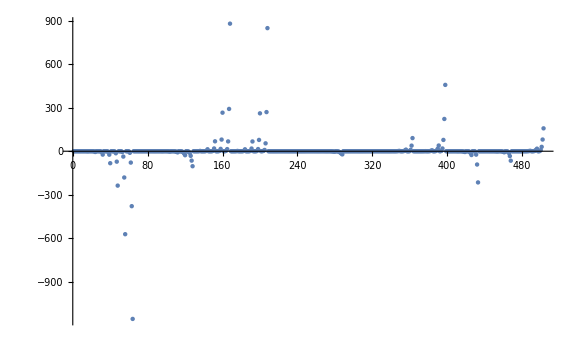
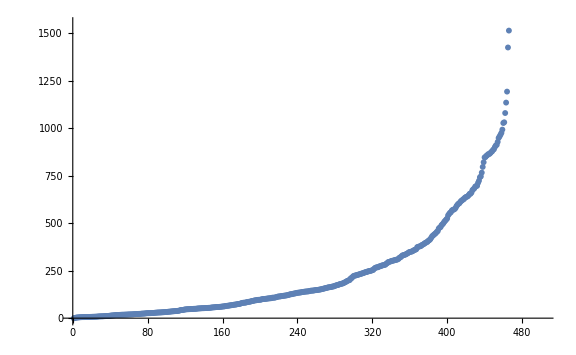
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[1]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYOut=Sort[Transpose[Eigensystem[{tst=(Transpose[LitNmhi].LitHam[[nj]]).LitNmhi;tst=(tst+Transpose[tst])/2,Transpose[LitNmhi].LitNorm[[nj]].LitNmhi}]],Re[#1[[1]]]<Re[#2[[1]]]&];

e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,LitNmh.v0l];
AppendTo[LitEigSys,orderedEVSYOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,Automatic},{-4,Automatic}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt;
tmp =BinaryReadList[fntmp,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
Print[Dimensions[tmp][[1]]];
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

144864

144864

Dim(⟨ψ|ο̂|helion⟩) = {1,503,288}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,503,503}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,503,503}

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};

{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};

Do[
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];

OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB]];
AppendTo[inhomoEB,Transpose[OμLHSEB].((tmp.OμRHSEB).evgsEB)];

{λfinal,trfLit}=Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}];
AppendTo[inhomo,tmp.evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

# of 2-1 states ≥ 1

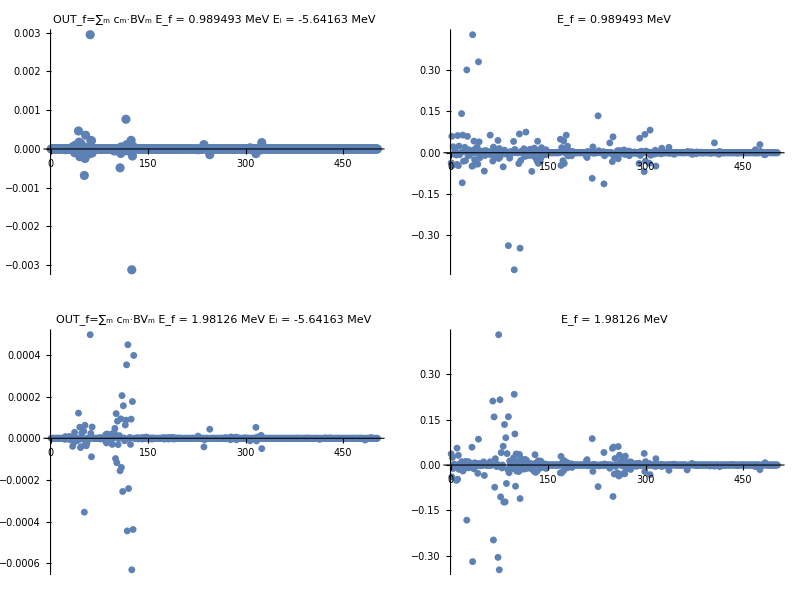

(1 | -0.0366614
2 | 0.0595269
3 | -0.0464026
4 | 0.0217024
10 | -0.0423013
11 | 0.0623892
12 | -0.0468321
13 | 0.0241557
17 | 0.141974
18 | -0.109018
19 | 0.0639853
20 | -0.0307127
23 | -0.0286311
25 | 0.300566
26 | 0.0593753
33 | -0.0488125
34 | 0.428362
35 | -0.0462461
36 | 0.0422237
37 | -0.0251169
41 | 0.0203782
42 | -0.041316
43 | 0.329916
44 | 0.0394896
52 | -0.0664973
61 | 0.0638608
65 | -0.0301416
66 | 0.0205199
73 | 0.0445623
74 | -0.0209091
81 | -0.0511672
89 | -0.337146
97 | 0.0409754
98 | -0.424791
105 | -0.0393783
106 | 0.0680303
107 | -0.346447
108 | -0.027855
116 | 0.0748837
125 | -0.0677171
133 | -0.0289444
134 | 0.0417078
135 | -0.0384636
138 | -0.0326544
169 | 0.0490907
170 | -0.0459119
173 | -0.0286876
174 | 0.0430813
175 | -0.0389513
178 | 0.0637119
180 | 0.0235503
218 | -0.092973
219 | 0.0211324
227 | 0.134002
236 | -0.113043
245 | 0.0356795
249 | -0.0322321
250 | 0.0577276
258 | -0.0217193
290 | -0.0390991
291 | 0.0525791
298 | -0.0684764
299 | 0.0665008
300 | -0.0298422
306 | -0.0382533
307 | 0.0821717
316 | -0.048489
406 | 0.0358144
476 | 0.0296447)(1 | 0.0370267
2 | -0.0389538
3 | 0.0251332
9 | -0.0507139
10 | 0.05608
11 | -0.0470602
12 | 0.0321537
25 | -0.182593
33 | 0.0590354
34 | -0.319935
42 | -0.0274448
43 | 0.085658
52 | -0.034526
65 | 0.211817
66 | -0.248288
67 | 0.159368
68 | -0.0735613
69 | 0.0208841
73 | -0.305805
74 | 0.431713
75 | -0.34701
76 | 0.216246
77 | -0.105465
78 | 0.0412051
81 | 0.0622146
82 | -0.122487
83 | 0.134185
84 | -0.122234
85 | 0.0903865
86 | -0.061133
87 | 0.0378572
89 | 0.160025
90 | -0.0252991
97 | 0.0237629
98 | 0.234283
99 | 0.103004
100 | -0.0702176
101 | 0.0368319
102 | -0.0204002
105 | -0.0213865
106 | 0.0351737
107 | -0.111105
108 | 0.0223995
129 | -0.0214466
130 | 0.0343364
131 | -0.024287
169 | -0.0259515
170 | 0.0285928
171 | -0.0257652
218 | 0.087367
219 | -0.021007
227 | -0.0716056
236 | 0.04157
249 | 0.0553091
250 | -0.104281
251 | 0.0596973
252 | -0.0297921
253 | 0.0216492
257 | -0.0262787
258 | 0.0612001
259 | -0.0362699
260 | 0.0327805
261 | -0.0320323
266 | -0.0283257
267 | 0.0211009
268 | -0.0290731
269 | 0.0294403
298 | 0.0383455
299 | -0.0215928
307 | -0.0318805
316 | 0.0210207)

-Graphics-1.04884×10^-7  ,  E_f=0.989493 MeV

-Graphics-1.04884×10^-7  ,  E_f=0.989493 MeV

```mathematica
OneTwoConti=Flatten[Position[λfinal,n_/;n<0]];
OrderedSpectF=Join[Delete[λfinal,{#}&/@OneTwoConti],Reverse[λfinal[[OneTwoConti]]]];
OrderedEvecsF=Join[Delete[trfLit,{#}&/@OneTwoConti],Reverse[trfLit[[OneTwoConti]]]];

Print["# of 2-1 states ≥ ",Length[OneTwoConti]]

contin=1;
evrng1={Length[OrderedSpectF]-contin};(*IntegerPart[Subdivide[1,Length[λfinal]-Length[OneTwoConti],20]];*)
evrng2={Length[OrderedSpectF]-contin-1};

inhomo1=(inhomo[[1]]  OrderedEvecsF[[#]])&/@evrng1;
FS1=OrderedEvecsF[[#]]&/@evrng1;
inhomo2=(inhomo[[1]]  OrderedEvecsF[[#]])&/@evrng2;
FS2=OrderedEvecsF[[#]]&/@evrng2;

Grid[{{
ListPlot[inhomo1,AxesLabel->{MaTeX["\\left\\vert\\text{BV}_m\\right\\rangle",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle\\text{BV}_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"OUT_f=∑_m c_m·BV_m  E_f = "<>ToString[OrderedSpectF[[evrng1[[1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV"],ListPlot[FS1,AxesLabel->{MaTeX["\\left\\vert\\text{BV}_m\\right\\rangle",Magnification->2],MaTeX["c_m=\\left\\langle BV_m\\Big\\vert\\text{OUT}_f\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f = "<>ToString[OrderedSpectF[[evrng1[[1]]]]]<>" MeV"]},{ListPlot[inhomo2,AxesLabel->{MaTeX["\\left\\vert\\text{BV}_m\\right\\rangle",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle\\text{BV}_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"OUT_f=∑_m c_m·BV_m  E_f = "<>ToString[OrderedSpectF[[evrng2[[1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV"],ListPlot[FS2,AxesLabel->{MaTeX["\\left\\vert\\text{BV}_m\\right\\rangle",Magnification->2],MaTeX["c_m=\\left\\langle BV_m\\Big\\vert\\text{OUT}_f\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f = "<>ToString[OrderedSpectF[[evrng2[[1]]]]]<>" MeV"]
}}
]
thc=0.02;
Print[Transpose[{Flatten[Position[Flatten[FS1],n_/;Abs[n]>thc]],FS1[[1]][[Flatten[Position[Flatten[FS1],n_/;Abs[n]>thc]]]]}]//MatrixForm
,
Transpose[{Flatten[Position[Flatten[FS2],n_/;Abs[n]>thc]],FS2[[1]][[Flatten[Position[Flatten[FS2],n_/;Abs[n]>thc]]]]}]//MatrixForm]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo1)^2)[[1]],"  ,  E_f=",OrderedSpectF[[evrng1[[1]]]]," MeV"]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo1)^2)[[-1]],"  ,  E_f=",OrderedSpectF[[evrng1[[-1]]]]," MeV"]
```

```mathematica
Print["Final-state structure: ",FinalStateLSdims];
typ=Table[FS1[[1]][[If[n==0,0,Accumulate[FinalStateLSdims][[n]]]+1;;Accumulate[FinalStateLSdims][[n+1]]]],{n,0,Length[FinalStateLSdims]-1}];
Print[Total[#]&/@typ];
typ=Table[FS2[[1]][[If[n==0,0,Accumulate[FinalStateLSdims][[n]]]+1;;Accumulate[FinalStateLSdims][[n+1]]]],{n,0,Length[FinalStateLSdims]-1}];
Print[Total[#]&/@typ];
```

Final-state structure: {64,64,40,40,40,40,40,35,35,35,35,35}

{1.09568,-1.09606,-0.0421509,0.0852771,-0.0376628,-0.0014602,-0.014908,0.0112577,0.00302753,0.034005,-0.00210709,0.0309506}

{-0.392312,0.395657,0.0118929,-0.0177757,0.0534514,0.00273106,0.0216838,-0.0135748,-0.0105022,-0.0115116,-0.000548132,-0.0119537}

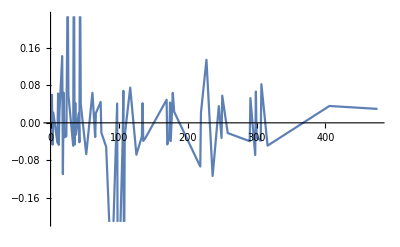

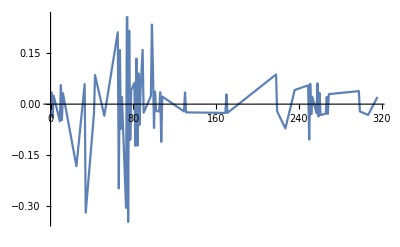

```mathematica
thc=0.02;
ListPlot[Transpose[{Flatten[Position[Flatten[FS1],n_/;Abs[n]>thc]],FS1[[1]][[Flatten[Position[Flatten[FS1],n_/;Abs[n]>thc]]]]}],Joined->True]
ListPlot[Transpose[{Flatten[Position[Flatten[FS2],n_/;Abs[n]>thc]],FS2[[1]][[Flatten[Position[Flatten[FS2],n_/;Abs[n]>thc]]]]}],Joined->True]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0^initial = -5.64163    dim(initial) = {288}

E_0^final  = -0.976121    dim(final)   = {503}

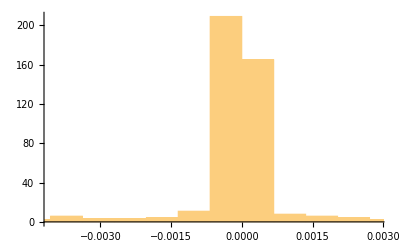

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[{(Transpose[OμRHSEV].He3Ham).OμRHSEV,(Transpose[OμRHSEV].He3Norm).OμRHSEV}];
EvecGSiEV=Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];

Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[{(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV,(Transpose[OμLHSEV].(LitNorm[[nj]])).OμLHSEV}];
EvecGSfEV=Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=(Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].OμRHSEV)).EvecGSiEV;
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsisEV,Re[Transpose[{EvalsFEV,tmplEV}]]];
AppendTo[CumStrengthsEV,Re[Transpose[{Sort[lpsisEV[[nj]]][[All,1]],Accumulate[Sort[lpsisEV[[nj]]][[All,2]]]}]]];

,{nj,Range[1,Length[Subscript[I, n]]]}
]
Histogram[Sort[EvecsFEV[[3]]]]
```

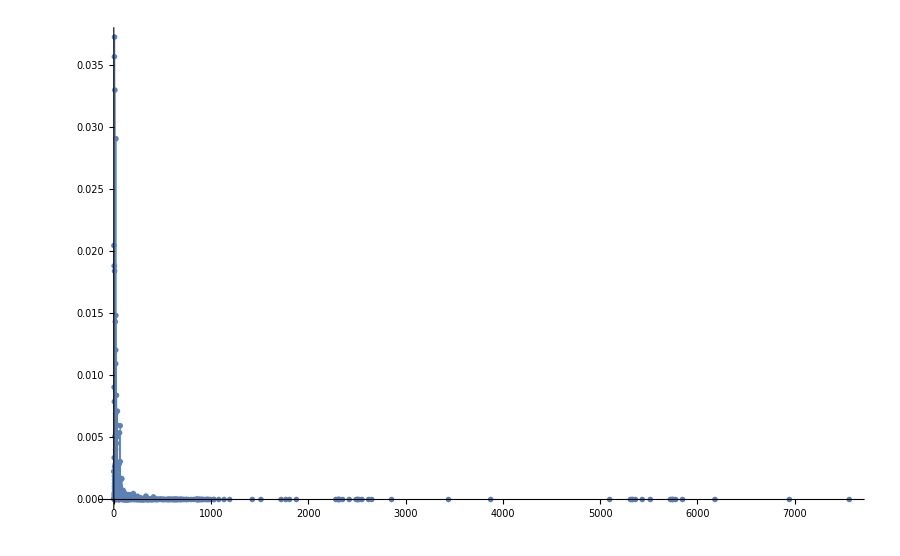
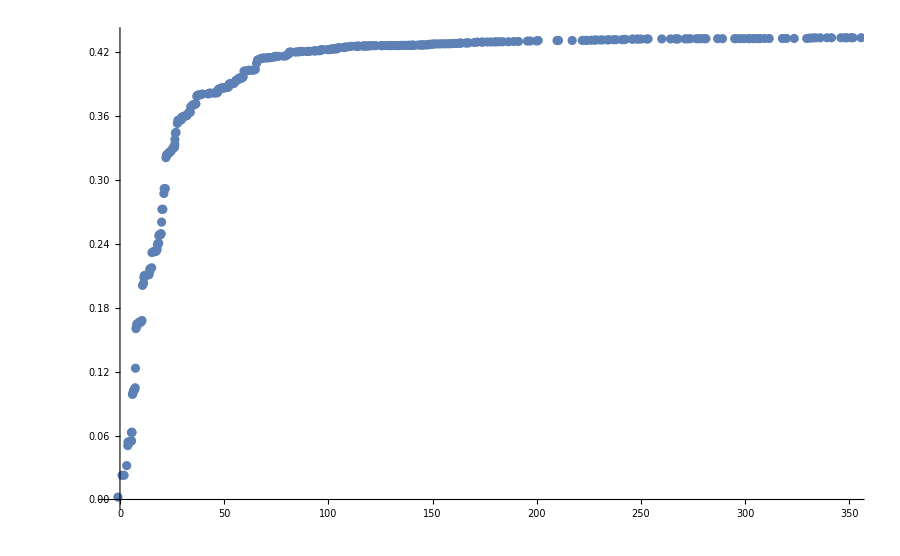
Grid[{-Graphics-,-Graphics-}]

Defficient LHS ME's: {222953}

Defficient RHS ME's: {80718}

```mathematica
plote3=Grid[{
ListPlot[Reverse[lpsisEV[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
,
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
}]
Print["Defficient LHS ME's: ",Dimensions[Select[Flatten[Chop[OμLHSEV.Transpose[OμLHSEV]]],#≠0.&&#≠1.&]]];
Print["Defficient RHS ME's: ",Dimensions[Select[Flatten[Chop[OμRHSEV.Transpose[OμRHSEV]]],#≠0.&&#≠1.&]]];
```

```mathematica
OrderedSpectF[[-11;;]]
```

{5.50406,5.47896,5.12566,4.96404,4.49918,3.84729,3.74265,3.22969,1.98126,0.989493,-0.976121}

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengthsEV,LocalObject["CumHelionStrengths_"<>StringTake[resultsDir,{-11,-9}]]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths_v24]

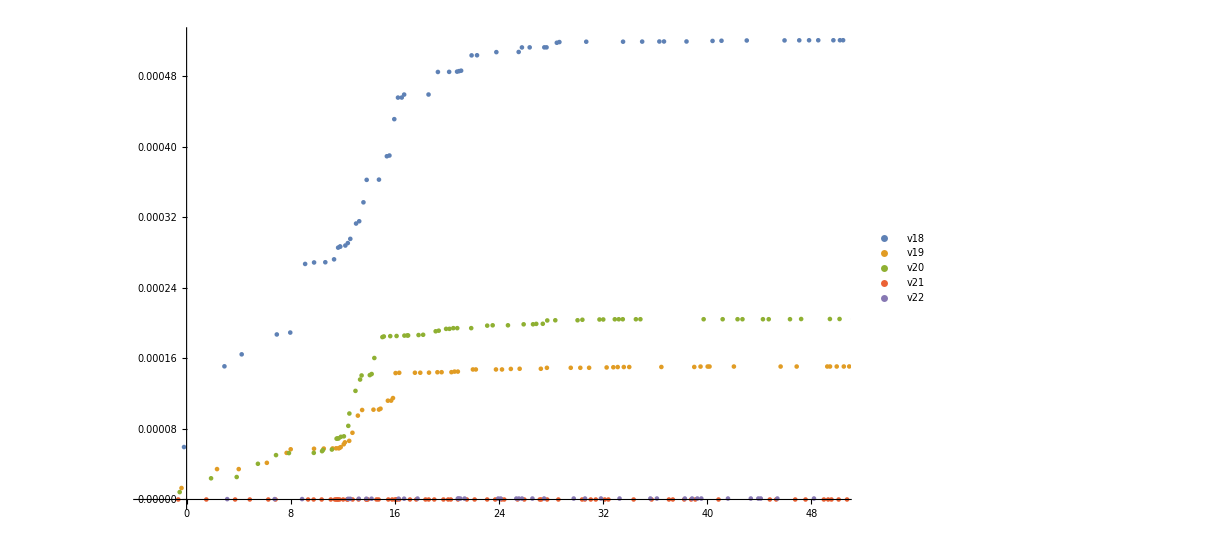

```mathematica
suffies={"v18","v19","v20","v21","v22"};
CumStrengthS={};
Do[
AppendTo[CumStrengthS,Flatten[Get[LocalObject["CumHelionStrengths_"<>suff]],1]];
,{suff,suffies}
]

ListPlot[CumStrengthS,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,50},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotLegends->suffies]
```